```mathematica
Quit[]
```

```mathematica
Needs["FeynArts`"]
Needs["FormCalc`"]
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (11 Dec 2021)

by Thomas Hahn

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
SetOptions[InsertFields, Model -> ToFileName[NotebookDirectory[],"modelFiles/SMS-stop_FA/SMS-stop_FA"],GenericModel->ToFileName[NotebookDirectory[],"modelFiles/LorentzTadpole"],ExcludeParticles->{S[1]}];
SetOptions[Paint, PaintLevel -> {Classes}];
```

```mathematica
FR$ClassesTranslation
```

{A→V[1],Z→V[2],W→V[3],G→V[4],ghA→U[1],ghZ→U[2],ghWp→U[3],ghWm→U[4],ghG→U[5],ve→F[1],vm→F[2],vt→F[3],e→F[4],mu→F[5],ta→F[6],u→F[7],c→F[8],t→F[9],d→F[10],s→F[11],b→F[12],H→S[1],G0→S[2],GP→S[3],chi→F[13],ST→S[4]}

```mathematica
processSMEFT = { V[4],V[4]} -> {-F[9], F[9]};
nameSMEFT = "SM-EFT";
topsSMEFT = CreateTopologies[1, 2-> 2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
insSMEFT = InsertFields[topsSMEFT, processSMEFT,InsertionLevel-> Particles,LastSelections->{S[4]}];
```

in total: 12 Generic, 13 Classes, 13 Particles insertions

```mathematica
processDMEFT = { V[4],V[4]} -> {F[13],F[13]};
nameDMEFT = "DM-EFT";
topsDMEFT = CreateTopologies[1, 2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
insDMEFT = InsertFields[topsDMEFT, processDMEFT,InsertionLevel-> Particles];
```

in total: 9 Generic, 18 Classes, 18 Particles insertions

```mathematica
processSMS = { V[4],V[4]} -> {F[13], F[13],-S[4],S[4]};
nameSMS = "SMS";
topsSMS = CreateTopologies[0, 2-> 4,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
insSMS = InsertFields[topsSMS, processSMS,InsertionLevel-> Particles];
```

in total: 34 Generic, 34 Classes, 34 Particles insertions

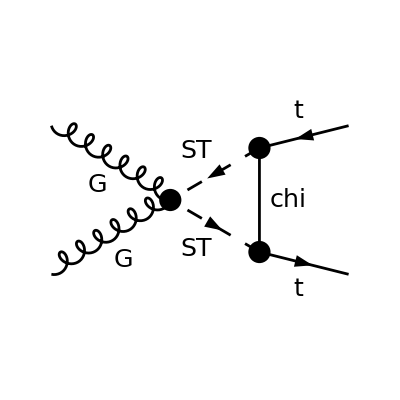

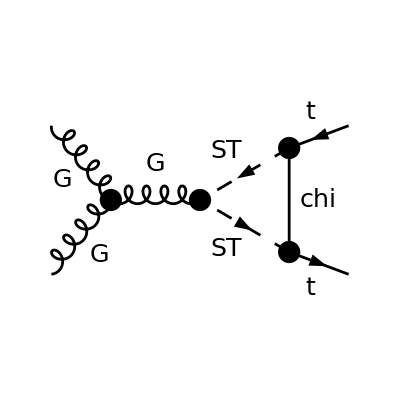

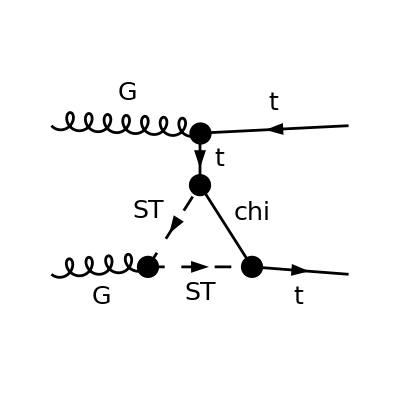

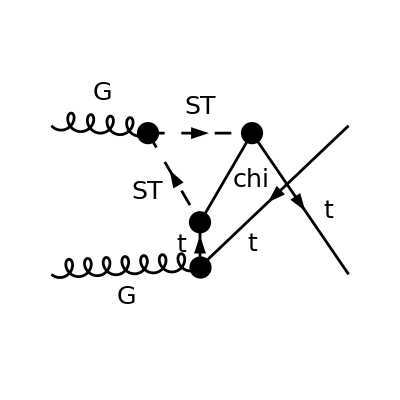

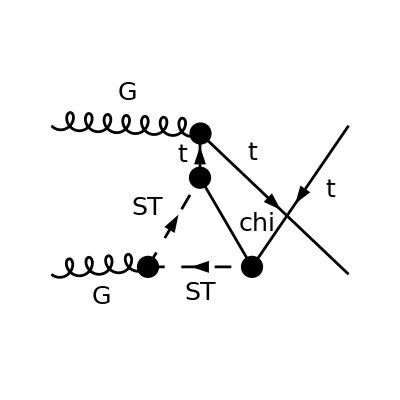

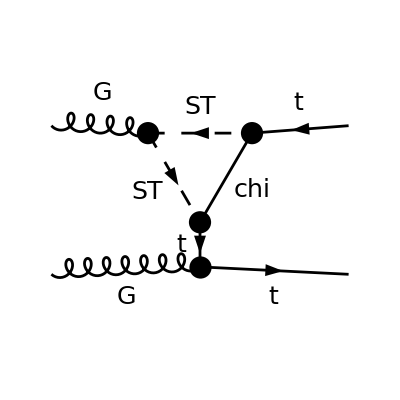

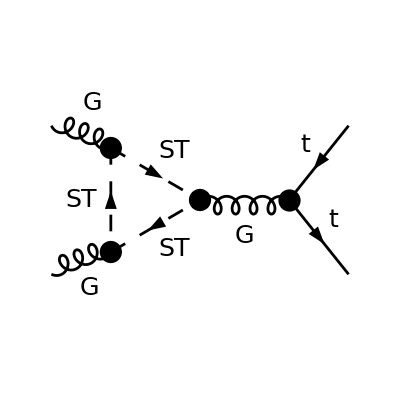

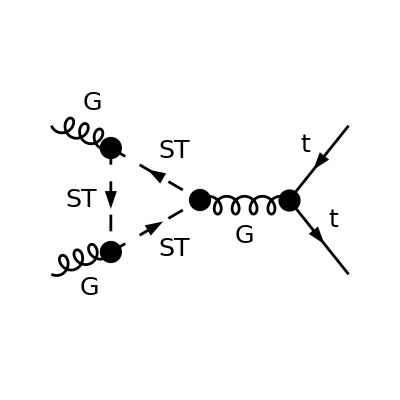

FeynArtsGraphics[SM-EFT][([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([])]

```mathematica
Paint[insSMEFT,ColumnsXRows->1,PaintLevel->{Classes},SheetHeader->nameSMEFT,Numbering->None,AutoEdit->True]
```

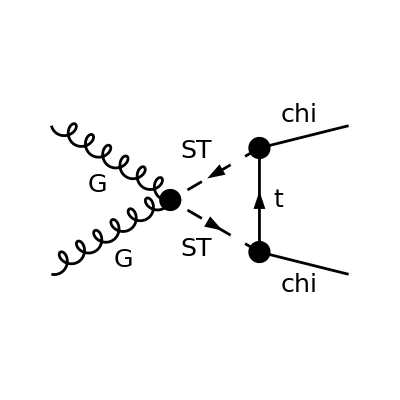

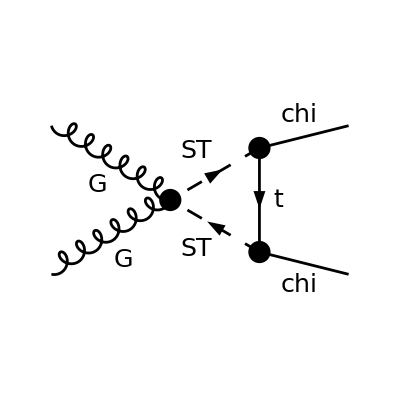

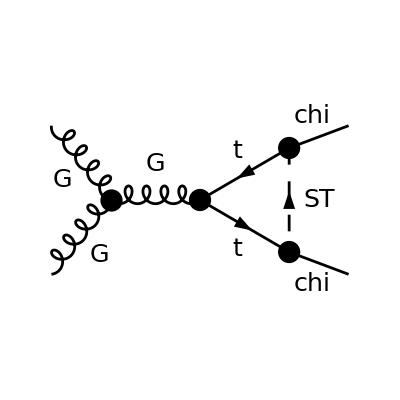

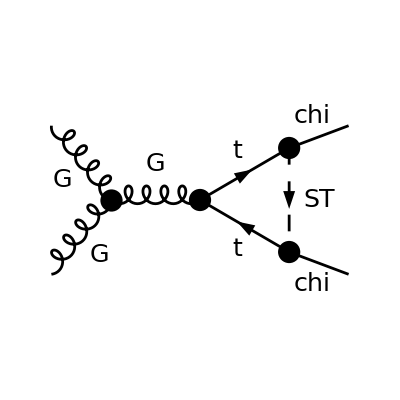

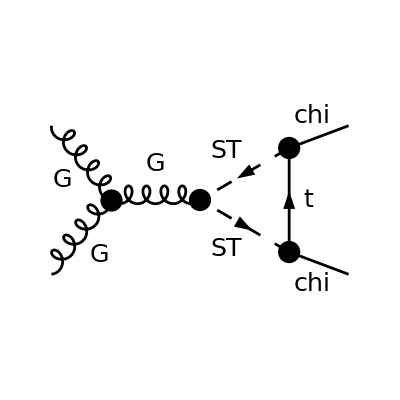

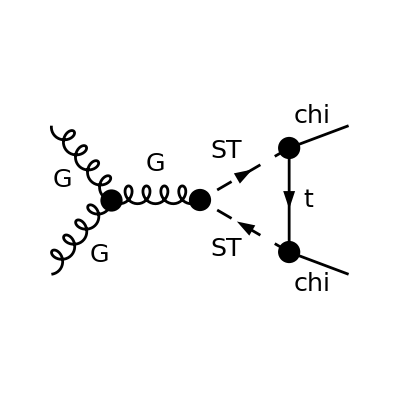

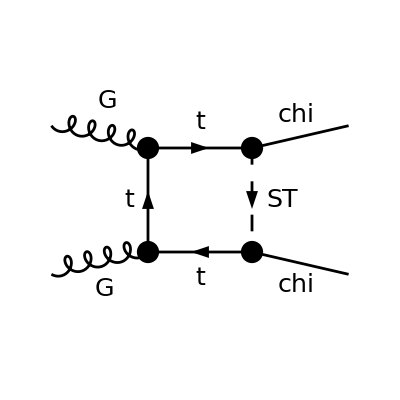

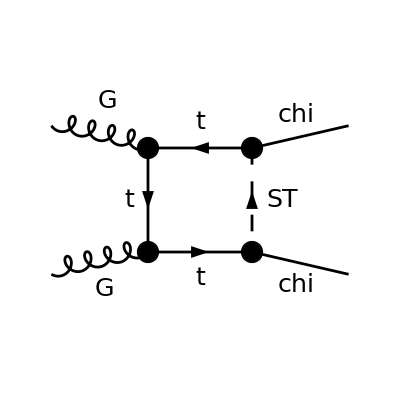

FeynArtsGraphics[DM-EFT][([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([])]

```mathematica
Paint[insDMEFT,ColumnsXRows->1,PaintLevel->{Classes},SheetHeader->nameDMEFT,Numbering->None,AutoEdit->True]
```

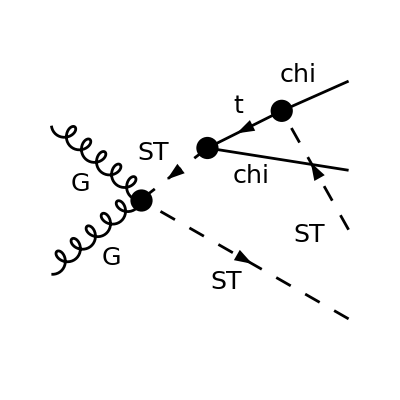

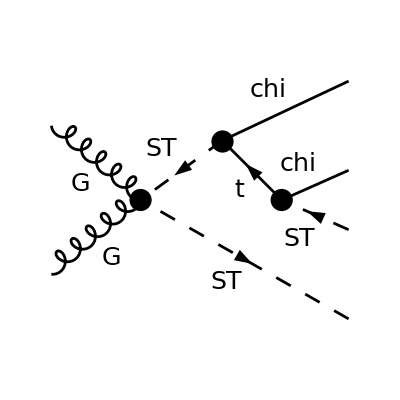

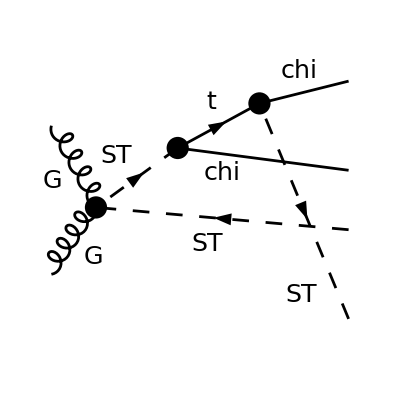

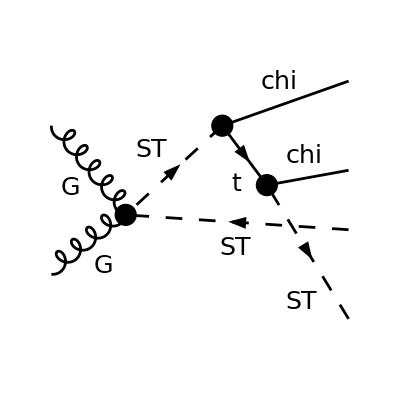

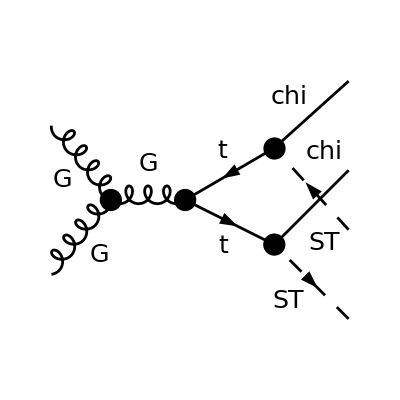

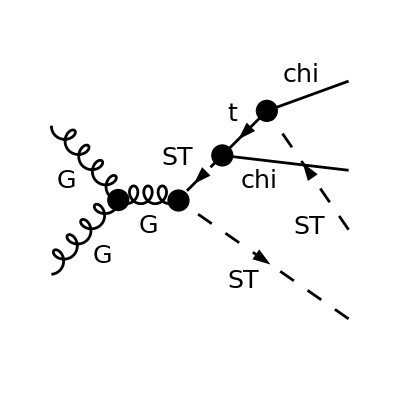

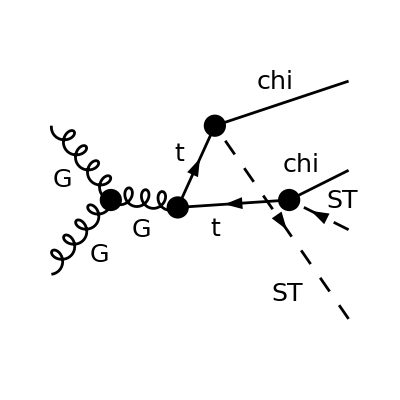

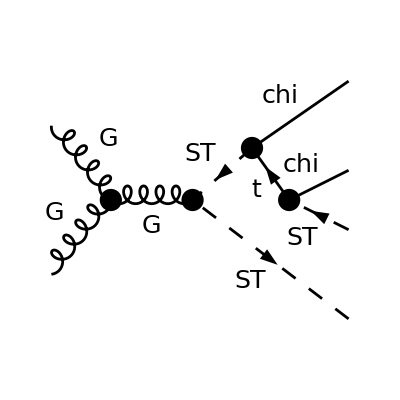

FeynArtsGraphics[SMS][([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([])]

```mathematica
Paint[insSMS,ColumnsXRows->1,PaintLevel->{Classes},SheetHeader->nameSMS,Numbering->None,AutoEdit->True]
```